Autor: Artur Bednarczyk

# Metody numeryczne w technice

## (kierunek informatyka)

## Projekt 8

Metoda różnic skończonych

Nieustalony przepływ ciepła (schemat jawny)

Napisać procedurę realizującą schemat jawny metody różnic skończonych dla zagadnienia nieustalonego przepływu ciepła:

c ρ (∂u)/(∂t)=λ (∂^2 u)/(∂x^2),   x∈(a,b),  t∈(0,t^*),

z warunkiem początkowym:

u(x,0) = u_0(x),

oraz warunkami brzegowymi pierwszego rodzaju:

u(a,t)=u_a(t),
u(b,t)=u_b(t).

Jako argument procedury należy podać liczbę nx węzłów siatki oraz czas końca t^*, natomiast krok czasu dt należy wyznaczyć (w programie) tak aby zapewnić stabilność obliczeń.

a) Korzystając z napisanej procedury wyznaczyć rozwiązanie przybliżone zagadnienia, w którym:

a=1, b=2,  t^*=1, 
c=1,  ρ=1, λ=1,

u_0(x)=x^3/6,
u_a(t)=t+1/6,
u_b(t)=2t+4/3.

Przedział [a,b] podzielić na 10 części.

Na wspólnym rysunku wykreślić rozwiązanie dokładne, którym jest funkcja u(x,t)=x^3/6+x t, oraz uzyskane rozwiązania przybliżone w chwili końcowej. Wykreślić także błędy uzyskanego rozwiązania przybliżonego w chwili końcowej.

## Rozwiązanie

```mathematica
ClearAll["Global`*"];
```

```mathematica
(* Nieustalony przepływ ciepła *)
npc[n_, t_]:=Module[{
a = 1,
b = 2,
c = 1,
p = 1,
λ = 1,
dt,tk,r,h, T,X,Y,
result, resultInT
},
h = (b-a)/n;
dt =(h^2*c*p)/(2*λ);
(* (h^2*c*p)/(2*λ);*)
tk = t/dt+1;
r = (λ*dt)/(c*p*h^2);
X=Table[a+h*i,{i,0,n}];
Y=Table[i*dt,{i,0,tk}];
T = Table[1,{i,tk}, {j, n+1}];
Do[T⟦1⟧⟦i⟧ = X⟦i⟧^3/6, {i,n+1}];
Do[T⟦i⟧⟦1⟧=Y⟦i⟧+1/6,{i,2,tk}];
Do[T⟦i⟧⟦n+1⟧=2*Y⟦i⟧+4/3,{i,2,tk}];
Do[
Do[
T⟦i⟧⟦j⟧ = T⟦i-1⟧⟦j⟧+r*(T⟦i-1⟧⟦j+1⟧-2*T⟦i-1⟧⟦j⟧+T⟦i-1⟧⟦j-1⟧);
,{j,2,n}];
,{i,2,tk}];
result = {
Table[{X⟦i⟧,Y⟦j⟧, T⟦j⟧⟦i⟧}, {i, 1, n+1}, {j,1,tk}],  Table[{X⟦i⟧, T⟦tk⟧⟦i⟧}, {i, 1, n+1}]
};
Return[result];
];
```

-Graphics3D-

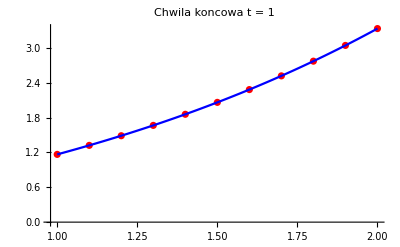

```mathematica
results=npc[10,1];
result =results⟦1⟧;
resultInT = results⟦2⟧;
Do[
AppendTo[resultInT, ]
,{i,1, Length[result]}];
resultFlat = Flatten[result, 1];
plt =Plot3D[x^3/6+x*t, {x,1,2},{t,0,1}, PlotStyle->Blue];
plt2 = Plot[x^3/6+x,{x,1,2}, PlotStyle->Blue];
resPlt = ListPlot3D[resultFlat, PlotStyle->Red];
resPlt2 = ListPlot[resultInT, PlotStyle->Red];
Show[resPlt, plt]
Show[resPlt2, plt2, PlotLabel->"Chwila koncowa t = 1 "]
```

-Graphics3D-

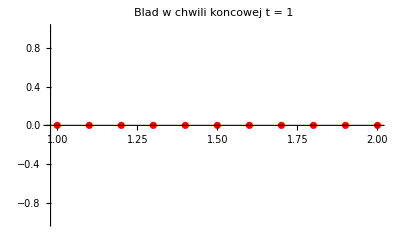

```mathematica
r = Table[{x,t,x^3/6+x*t},{x,1,2,1/10},{t,0,1,1/200}];
rInT = Table[{x, x^3/6+x}, {x,1,2,1/10}];

rFlat =Flatten[r,1];

errors = Table[
{resultFlat⟦i,1⟧,
  resultFlat⟦i,2⟧,
Abs[rFlat⟦i,3⟧-resultFlat⟦i,3⟧]},
{i,1,Min[Length[rFlat], Length[resultFlat]]}];
ListPlot3D[errors, PlotStyle->Red]

errorsInT = Table[{resultInT⟦i,1⟧, Abs[resultInT⟦i,2⟧ - rInT⟦i,2⟧]},{i,1,Min[Length[rInT],Length[resultInT]]}];
ListPlot[errorsInT, PlotStyle->Red,PlotRange->All, PlotLabel->"Blad w chwili koncowej t = 1 "]
```